This implements some stuff from Sawin' s wonderful paper!

```mathematica
QuantumGroupsPath = "c:\\scott\\projects\\QuantumGroups\\trunk\\package\\";
AppendTo[$Path, QuantumGroupsPath];
<<QuantumGroups`
```

Loading QuantumGroups` version 2.0
Read more at http://katlas.math.toronto.edu/wiki/QuantumGroups

Found precomputed data in C:\scott\projects\QuantumGroups\trunk\data

General::obspkg: "LinearAlgebra`MatrixManipulation`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
ρ[Γ_]:=(Plus@@PositiveRoots[Γ])/2
```

```mathematica
ShortDominantRoots[G2]
```

{{1,0}}

```mathematica
LongDominantRoots[G2]
```

{{0,1}}

```mathematica
LacingNumber[Subscript[(A|D|E), _]]=1;
LacingNumber[Subscript[(B|C|F), _]]=2;
LacingNumber[Subscript[G, 2]]=3;
```

```mathematica
AlcoveRoot[Γ_,l_]:=With[{lp=If[EvenQ[l],l/2,l]},
If[Divisible[lp,LacingNumber[Γ]],
LongDominantRoots[Γ]⟦1⟧,
ShortDominantRoots[Γ]⟦1⟧]
]
```

```mathematica
AlcoveRoot[G2,26]
```

{1,0}

```mathematica
WeightInAlcoveQ[Γ_,l_Integer][λ:{___Integer}]:=(And@@(NonNegative/@λ))∧(KillingForm[Γ][AlcoveRoot[Γ,l],λ+ρ[Γ]]<If[EvenQ[l],l/2,l])
```

```mathematica
AlcoveWeights[Γ_,l_]:=AlcoveWeights[Γ,l]=Module[{ar=AlcoveRoot[Γ,l],λ=ZeroVector[Rank[Γ]],p},
Reap[
While[
Sow[λ];
λ+=UnitVector[Rank[Γ],1];
While[¬ZeroVectorQ[λ]∧¬WeightInAlcoveQ[Γ,l][λ],
(* odometer *)
p=Position[λ,x_/;x>0]⟦1,1⟧;
λ⟦p⟧=0;
If[p<Rank[Γ],++λ⟦p+1⟧];
];
¬ZeroVectorQ[λ]
]
]⟦2,1⟧
]
```

```mathematica
AlcoveWeights[G2,26]
```

{{0,0},{1,0},{2,0},{3,0},{0,1},{1,1},{2,1},{0,2}}

```mathematica
Chop[N[(qDimension[G2][Irrep[G2][#]]&/@AlcoveWeights[G2,26])/.q->Exp[2π ⅈ 1/26]]]
```

{1.,0.564681,-0.400477,1.09654,-0.845339,-0.64155,0.564681,-0.136129}

```mathematica
Chop[N[(qDimension[G2][Irrep[G2][#]]&/@AlcoveWeights[G2,26])/.q->Exp[2π ⅈ 3/26]]]
```

{1.,4.14811,7.34595,6.20982,4.7128,8.05516,4.14811,2.94188}

```mathematica
Length[AlcoveWeights[G2,28]]
```

10

```mathematica
Chop[N[(qDimension[G2][Irrep[G2][#]]&/@AlcoveWeights[G2,28])/.q->Exp[2π ⅈ 3/28]]]
```

{1.,4.49396,9.09783,10.0978,4.49396,5.60388,11.5918,10.0978,5.60388,3.49396}

```mathematica
Chop[N[(qDimension[G2][Irrep[G2][#]]&/@AlcoveWeights[G2,28])/.q->Exp[2π ⅈ 11/28]]]
```

{1.,4.49396,9.09783,10.0978,4.49396,5.60388,11.5918,10.0978,5.60388,3.49396}

```mathematica
Min[DeleteCases[%,1.]]
```

3.49396

```mathematica
FullSimplify[Last[(qDimension[G2][Irrep[G2][#]]&/@AlcoveWeights[G2,28])/.q->Exp[2π ⅈ 11/28]]]
```

2 (Cos[π/7]+Sin[π/14]+Sin[(3 π)/14])

```mathematica
FullSimplify[δ/.Solve[δ^2-1==%,δ]⟦2⟧]
```

√(1+2 (Cos[π/7]+Sin[π/14]+Sin[(3 π)/14]))

```mathematica
N[%]
```

2.1199

```mathematica
Table[Length[AlcoveWeights[G2,l]],{l,24,30}]
```

{1,40,8,12,10,56,2}

```mathematica
Table[Length[AlcoveWeights[G2,l]],{l,24,60}]
```

{1,40,8,12,10,56,2,65,14,20,16,85,4,96,21,30,24,120,6,133,30,42,33,161,9,176,40,56,44,208,12,225,52,72,56,261,16}

```mathematica
Range[4]
```

{1,2,3,4}

```mathematica
PositiveDimensionNumerators[Γ_,l_]:=Cases[Cases[Range[l]-1,k_/;CoprimeQ[l,k]],k_/;And@@(Positive/@Chop[N[(qDimension[Γ][Irrep[Γ][#]]&/@AlcoveWeights[Γ,l])/.q->Exp[2π ⅈ k/l]]])]
```

```mathematica
Table[{l,Length[AlcoveWeights[G2,l]],{PositiveDimensionNumerators[G2,l]}},{l,1,11}]//TableForm
```

1 | 1 | 0
2 | 1 | 1
3 | 1 | 1 | 2
4 | 1 | 1 | 3
5 | 1 | 1 | 2 | 3 | 4
6 | 1 | 1 | 5
7 | 1 | 1 | 2 | 3 | 4 | 5 | 6
8 | 1 | 1 | 3 | 5 | 7
9 | 1 | 1 | 2 | 4 | 5 | 7 | 8
10 | 1 | 1 | 3 | 7 | 9
11 | 5 | 1 | 10

```mathematica
Table[{l,Length[AlcoveWeights[G2,l]],{PositiveDimensionNumerators[G2,l]}},{l,12,23}]//TableForm
```

12 | 1 | 1 | 5 | 7 | 11
13 | 8 | 5 | 8
14 | 1 | 1 | 3 | 5 | 9 | 11 | 13
15 | 2 | 2 | 7 | 8 | 13
16 | 2 | 
17 | 16 | 
18 | 1 | 1 | 5 | 7 | 11 | 13 | 17
19 | 21 | 
20 | 4 | 
21 | 6 | 2 | 8 | 10 | 11 | 13 | 19
22 | 5 | 9 | 13
23 | 33 |

```mathematica
Table[{l,Length[AlcoveWeights[G2,l]],{PositiveDimensionNumerators[G2,l]}},{l,24,40}]//TableForm
```

24 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23
25 | 40 | 
26 | 8 | 3 | 23
27 | 12 | 13 | 14
28 | 10 | 3 | 11 | 17 | 25
29 | 56 | 
30 | 2 | 1 | 11 | 19 | 29
31 | 65 | 
32 | 14 | 
33 | 20 | 16 | 17
34 | 16 | 
35 | 85 | 
36 | 4 | 1 | 17 | 19 | 35
37 | 96 | 
38 | 21 | 
39 | 30 | 19 | 20
40 | 24 |

```mathematica
Table[{l,Length[AlcoveWeights[G2,l]],{PositiveDimensionNumerators[G2,l]}},{l,41,50}]//TableForm
```

41 | 120 | 
42 | 6 | 1 | 5 | 17 | 25 | 37 | 41
43 | 133 | 
44 | 30 | 
45 | 42 | 22 | 23
46 | 33 | 
47 | 161 | 
48 | 9 | 1 | 5 | 19 | 23 | 25 | 29 | 43 | 47
49 | 176 | 
50 | 40 |

```mathematica
Chop[N[(qDimension[G2][Irrep[G2][#]]&/@AlcoveWeights[G2,42])/.q->Exp[2π ⅈ 1/42]]]
```

{1.,3.79129,5.79129,3.79129,3.79129,4.79129}

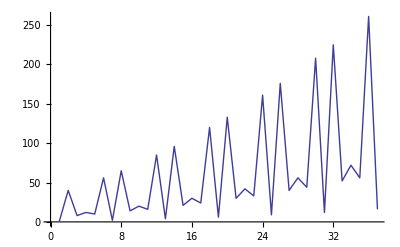

```mathematica
ListPlot[Table[Length[AlcoveWeights[G2,l]],{l,24,60}],"PlotJoined"->True]
```

```mathematica
Table[{l,Length[AlcoveWeights[A2,l]],{PositiveDimensionNumerators[A2,l]}},{l,1,20}]//TableForm
```

1 | 1 | 0
2 | 1 | 1
3 | 1 | 1 | 2
4 | 1 | 1 | 3
5 | 6 | 2 | 3
6 | 1 | 1 | 5
7 | 15 | 3 | 4
8 | 3 | 1 | 3 | 5 | 7
9 | 28 | 4 | 5
10 | 6 | 1 | 9
11 | 45 | 5 | 6
12 | 10 | 1 | 5 | 7 | 11
13 | 66 | 6 | 7
14 | 15 | 1 | 13
15 | 91 | 7 | 8
16 | 21 | 1 | 7 | 9 | 15
17 | 120 | 8 | 9
18 | 28 | 1 | 17
19 | 153 | 9 | 10
20 | 36 | 1 | 9 | 11 | 19

```mathematica
Chop[N[(qDimension[A2][Irrep[A2][#]]&/@AlcoveWeights[A2,7])/.q->Exp[2π ⅈ 3/7]]]
```

{1.,2.24698,2.80194,2.24698,1.,2.24698,4.04892,4.04892,2.24698,2.80194,4.04892,2.80194,2.24698,2.24698,1.}

```mathematica
%^2
```

{1.,5.04892,7.85086,5.04892,1.,5.04892,16.3937,16.3937,5.04892,7.85086,16.3937,7.85086,5.04892,5.04892,1.}

```mathematica
Table[{l,Length[AlcoveWeights[A3,l]],{PositiveDimensionNumerators[A3,l]}},{l,1,20}]//TableForm
```

1 | 1 | 0
2 | 1 | 1
3 | 1 | 1 | 2
4 | 1 | 1 | 3
5 | 4 | 
6 | 1 | 1 | 5
7 | 20 | 
8 | 1 | 1 | 3 | 5 | 7
9 | 56 | 
10 | 4 | 1 | 3 | 7 | 9
11 | 120 | 
12 | 10 | 1 | 11
13 | 220 | 
14 | 20 | 1 | 13
15 | 364 | 
16 | 35 | 1 | 15
17 | 560 | 
18 | 56 | 1 | 17
19 | 816 | 
20 | 84 | 1 | 19

```mathematica
Table[{l,Length[AlcoveWeights[A4,l]],{PositiveDimensionNumerators[A4,l]}},{l,1,20}]//TableForm
```

1 | 1 | 0
2 | 1 | 1
3 | 1 | 1 | 2
4 | 1 | 1 | 3
5 | 1 | 1 | 2 | 3 | 4
6 | 1 | 1 | 5
7 | 15 | 3 | 4
8 | 1 | 1 | 3 | 5 | 7
9 | 70 | 4 | 5
10 | 1 | 1 | 3 | 7 | 9
11 | 210 | 5 | 6
12 | 5 | 1 | 5 | 7 | 11
13 | 495 | 6 | 7
14 | 15 | 1 | 13
15 | 1001 | 7 | 8
16 | 35 | 1 | 7 | 9 | 15
17 | 1820 | 8 | 9
18 | 70 | 1 | 17
19 | 3060 | 9 | 10
20 | 126 | 1 | 9 | 11 | 19

```mathematica
DualCoxeterNumber[D4]
```

6

```mathematica
Table[{l,Length[AlcoveWeights[D4,l]],{PositiveDimensionNumerators[D4,l]}},{l,1,20}]//TableForm
```

1 | 1 | 0
2 | 1 | 1
3 | 1 | 1 | 2
4 | 1 | 1 | 3
5 | 1 | 1 | 2 | 3 | 4
6 | 1 | 1 | 5
7 | 4 | 1 | 2 | 3 | 4 | 5 | 6
8 | 1 | 1 | 3 | 5 | 7
9 | 24 | 4 | 5
10 | 1 | 1 | 3 | 7 | 9
11 | 80 | 5 | 6
12 | 1 | 1 | 5 | 7 | 11
13 | 200 | 6 | 7
14 | 4 | 1 | 3 | 5 | 9 | 11 | 13
15 | 420 | 7 | 8
16 | 11 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
17 | 784 | 8 | 9
18 | 24 | 1 | 17
19 | 1344 | 9 | 10
20 | 46 | 1 | 9 | 11 | 19

```mathematica
Chop[N[(qDimension[D4][Irrep[D4][#]]&/@AlcoveWeights[D4,7])/.q->Exp[2π ⅈ 3/7]]]
```

{1.,1.,1.,1.}

```mathematica
Chop[N[(qDimension[D4][Irrep[D4][#]]&/@AlcoveWeights[D4,9])/.q->Exp[2π ⅈ 4/9]]]
```

{1.,2.87939,2.87939,1.,4.41147,4.41147,2.87939,5.41147,2.87939,4.41147,2.87939,2.87939,1.,2.87939,5.41147,2.87939,4.41147,5.41147,5.41147,2.87939,2.87939,2.87939,2.87939,1.}

```mathematica
DualCoxeterNumber[B2]
```

3

```mathematica
Table[{l,Length[AlcoveWeights[B2,l]],{PositiveDimensionNumerators[B2,l]}},{l,1,20}]//TableForm
```

1 | 1 | 0
2 | 1 | 1
3 | 1 | 1 | 2
4 | 1 | 1 | 3
5 | 2 | 
6 | 1 | 1 | 5
7 | 6 | 
8 | 1 | 1 | 3 | 5 | 7
9 | 12 | 
10 | 2 | 
11 | 20 | 
12 | 1 | 1 | 5 | 7 | 11
13 | 30 | 
14 | 6 | 
15 | 42 | 
16 | 3 | 1 | 7 | 9 | 15
17 | 56 | 
18 | 12 | 
19 | 72 | 
20 | 6 | 1 | 9 | 11 | 19

```mathematica
Table[{l,Length[AlcoveWeights[B2,l]],{PositiveDimensionNumerators[B2,l]}},{l,21,40}]//TableForm
```

21 | 90 | 
22 | 20 | 
23 | 110 | 
24 | 10 | 1 | 11 | 13 | 23
25 | 132 | 
26 | 30 | 
27 | 156 | 
28 | 15 | 1 | 13 | 15 | 27
29 | 182 | 
30 | 42 | 
31 | 210 | 
32 | 21 | 1 | 15 | 17 | 31
33 | 240 | 
34 | 56 | 
35 | 272 | 
36 | 28 | 1 | 17 | 19 | 35
37 | 306 | 
38 | 72 | 
39 | 342 | 
40 | 36 | 1 | 19 | 21 | 39

```mathematica
Table[{l,Length[AlcoveWeights[B3,l]],{PositiveDimensionNumerators[B3,l]}},{l,1,20}]//TableForm
```

1 | 1 | 0
2 | 1 | 1
3 | 1 | 1 | 2
4 | 1 | 1 | 3
5 | 1 | 1 | 2 | 3 | 4
6 | 1 | 1 | 5
7 | 2 | 1 | 2 | 3 | 4 | 5 | 6
8 | 1 | 1 | 3 | 5 | 7
9 | 8 | 1 | 8
10 | 1 | 1 | 3 | 7 | 9
11 | 20 | 
12 | 1 | 1 | 5 | 7 | 11
13 | 40 | 
14 | 2 | 
15 | 70 | 
16 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
17 | 112 | 
18 | 8 | 
19 | 168 | 
20 | 1 | 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19

```mathematica
Chop[N[(qDimension[B3][Irrep[B3][#]]&/@AlcoveWeights[B3,14])/.q->Exp[2π ⅈ 1/14]]]
```

{1.,-1.}

```mathematica
Chop[N[(qDimension[B3][Irrep[B3][#]]&/@AlcoveWeights[B3,18])/.q->Exp[2π ⅈ 3/18]]]
```

{1.,1.,0,-2.,0,2.,2.,-4.}

```mathematica
Table[{l,Length[AlcoveWeights[B3,l]],{PositiveDimensionNumerators[B3,l]}},{l,22,40,2}]//TableForm
```

22 | 20 | 
24 | 3 | 1 | 7 | 17 | 23
26 | 40 | 
28 | 7 | 1 | 3 | 9 | 19 | 25 | 27
30 | 70 | 
32 | 13 | 1 | 31
34 | 112 | 
36 | 22 | 1 | 35
38 | 168 | 
40 | 34 | 1 | 39

```mathematica
DualCoxeterNumber[B4]
```

7

```mathematica
Table[{l,Length[AlcoveWeights[B4,l]],{PositiveDimensionNumerators[B4,l]}},{l,2,20,1}]//TableForm
```

2 | 1 | 1
3 | 1 | 1 | 2
4 | 1 | 1 | 3
5 | 1 | 1 | 2 | 3 | 4
6 | 1 | 1 | 5
7 | 1 | 1 | 2 | 3 | 4 | 5 | 6
8 | 1 | 1 | 3 | 5 | 7
9 | 2 | 1 | 2 | 4 | 5 | 7 | 8
10 | 1 | 1 | 3 | 7 | 9
11 | 10 | 4 | 7
12 | 1 | 1 | 5 | 7 | 11
13 | 30 | 
14 | 1 | 1 | 3 | 5 | 9 | 11 | 13
15 | 70 | 
16 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
17 | 140 | 
18 | 2 | 1 | 5 | 7 | 11 | 13 | 17
19 | 252 | 
20 | 1 | 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19

```mathematica
Table[{l,Length[AlcoveWeights[B4,l]],{PositiveDimensionNumerators[B4,l]}},{l,2,40,2}]//TableForm
```

2 | 1 | 1
4 | 1 | 1 | 3
6 | 1 | 1 | 5
8 | 1 | 1 | 3 | 5 | 7
10 | 1 | 1 | 3 | 7 | 9
12 | 1 | 1 | 5 | 7 | 11
14 | 1 | 1 | 3 | 5 | 9 | 11 | 13
16 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
18 | 2 | 1 | 5 | 7 | 11 | 13 | 17
20 | 1 | 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19
22 | 10 | 3 | 19
24 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23
26 | 30 | 
28 | 1 | 1 | 3 | 5 | 9 | 11 | 13 | 15 | 17 | 19 | 23 | 25 | 27
30 | 70 | 
32 | 3 | 1 | 7 | 9 | 15 | 17 | 23 | 25 | 31
34 | 140 | 
36 | 8 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23 | 25 | 29 | 31 | 35
38 | 252 | 
40 | 16 | 1 | 19 | 21 | 39

```mathematica
Chop[N[(qDimension[B4][Irrep[B4][#]]&/@AlcoveWeights[B4,18])/.q->Exp[2π ⅈ 1/18]]]
```

{1.,1.}

```mathematica
Chop[N[(qDimension[B4][Irrep[B4][#]]&/@AlcoveWeights[B4,22])/.q->Exp[2π ⅈ 3/22]]]
```

{1.,1.91899,2.68251,3.22871,3.51334,3.22871,2.68251,1.91899,3.51334,1.}

```mathematica
Chop[N[(qDimension[B5][Irrep[B5][#]]&/@AlcoveWeights[B5,22])/.q->Exp[2π ⅈ 1/22]]]
```

{1.,1.}

```mathematica
Chop[N[(qDimension[B5][Irrep[B5][#]]&/@AlcoveWeights[B5,26])/.q->Exp[2π ⅈ 3/26]]]
```

{1.,1.94188,2.77091,3.43891,3.90704,4.14811,3.90704,3.43891,2.77091,1.94188,4.14811,1.}

```mathematica
Chop[N[(qDimension[B6][Irrep[B6][#]]&/@AlcoveWeights[B6,30])/.q->Exp[2π ⅈ 3/30]]]
```

{1.,1.61803,1.61803,1.,0,2.,-3.23607,-2.,0,2.,3.23607,-6.47214,3.23607,-4.}

```mathematica
Chop[N[(qDimension[B7][Irrep[B7][#]]&/@AlcoveWeights[B7,34])/.q->Exp[2π ⅈ 3/34]]]
```

$Aborted

```mathematica
Table[{l,Length[AlcoveWeights[B5,l]],{PositiveDimensionNumerators[B5,l]}},{l,2,20,1}]//TableForm
```

2 | 1 | 1
3 | 1 | 1 | 2
4 | 1 | 1 | 3
5 | 1 | 1 | 2 | 3 | 4
6 | 1 | 1 | 5
7 | 1 | 1 | 2 | 3 | 4 | 5 | 6
8 | 1 | 1 | 3 | 5 | 7
9 | 1 | 1 | 2 | 4 | 5 | 7 | 8
10 | 1 | 1 | 3 | 7 | 9
11 | 2 | 
12 | 1 | 1 | 5 | 7 | 11
13 | 12 | 
14 | 1 | 1 | 3 | 5 | 9 | 11 | 13
15 | 42 | 
16 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
17 | 112 | 
18 | 1 | 1 | 5 | 7 | 11 | 13 | 17
19 | 252 | 
20 | 1 | 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19

```mathematica
Table[{l,Length[AlcoveWeights[B5,l]],{PositiveDimensionNumerators[B5,l]}},{l,2,40,2}]//TableForm
```

2 | 1 | 1
4 | 1 | 1 | 3
6 | 1 | 1 | 5
8 | 1 | 1 | 3 | 5 | 7
10 | 1 | 1 | 3 | 7 | 9
12 | 1 | 1 | 5 | 7 | 11
14 | 1 | 1 | 3 | 5 | 9 | 11 | 13
16 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
18 | 1 | 1 | 5 | 7 | 11 | 13 | 17
20 | 1 | 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19
22 | 2 | 1 | 3 | 5 | 7 | 9 | 13 | 15 | 17 | 19 | 21
24 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23
26 | 12 | 3 | 23
28 | 1 | 1 | 3 | 5 | 9 | 11 | 13 | 15 | 17 | 19 | 23 | 25 | 27
30 | 42 | 
32 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 29 | 31
34 | 112 | 
36 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23 | 25 | 29 | 31 | 35
38 | 252 | 
40 | 3 | 1 | 7 | 9 | 17 | 23 | 31 | 33 | 39

```mathematica
Table[{l,Length[AlcoveWeights[B6,l]],{PositiveDimensionNumerators[B6,l]}},{l,2,20,1}]//TableForm
```

2 | 1 | 1
3 | 1 | 1 | 2
4 | 1 | 1 | 3
5 | 1 | 1 | 2 | 3 | 4
6 | 1 | 1 | 5
7 | 1 | 1 | 2 | 3 | 4 | 5 | 6
8 | 1 | 1 | 3 | 5 | 7
9 | 1 | 1 | 2 | 4 | 5 | 7 | 8
10 | 1 | 1 | 3 | 7 | 9
11 | 1 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
12 | 1 | 1 | 5 | 7 | 11
13 | 2 | 
14 | 1 | 1 | 3 | 5 | 9 | 11 | 13
15 | 14 | 
16 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
17 | 56 | 
18 | 1 | 1 | 5 | 7 | 11 | 13 | 17
19 | 168 | 
20 | 1 | 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19

```mathematica
Table[{l,Length[AlcoveWeights[B6,l]],{PositiveDimensionNumerators[B6,l]}},{l,2,40,2}]//TableForm
```

2 | 1 | 1
4 | 1 | 1 | 3
6 | 1 | 1 | 5
8 | 1 | 1 | 3 | 5 | 7
10 | 1 | 1 | 3 | 7 | 9
12 | 1 | 1 | 5 | 7 | 11
14 | 1 | 1 | 3 | 5 | 9 | 11 | 13
16 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
18 | 1 | 1 | 5 | 7 | 11 | 13 | 17
20 | 1 | 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19
22 | 1 | 1 | 3 | 5 | 7 | 9 | 13 | 15 | 17 | 19 | 21
24 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23
26 | 2 | 
28 | 1 | 1 | 3 | 5 | 9 | 11 | 13 | 15 | 17 | 19 | 23 | 25 | 27
30 | 14 | 
32 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 29 | 31
34 | 56 | 
36 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23 | 25 | 29 | 31 | 35
38 | 168 | 
40 | 1 | 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19 | 21 | 23 | 27 | 29 | 31 | 33 | 37 | 39

```mathematica
Table[{l,Length[AlcoveWeights[B7,l]],{PositiveDimensionNumerators[B7,l]}},{l,2,34,2}]//TableForm
```

2 | 1 | 1
4 | 1 | 1 | 3
6 | 1 | 1 | 5
8 | 1 | 1 | 3 | 5 | 7
10 | 1 | 1 | 3 | 7 | 9
12 | 1 | 1 | 5 | 7 | 11
14 | 1 | 1 | 3 | 5 | 9 | 11 | 13
16 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
18 | 1 | 1 | 5 | 7 | 11 | 13 | 17
20 | 1 | 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19
22 | 1 | 1 | 3 | 5 | 7 | 9 | 13 | 15 | 17 | 19 | 21
24 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23
26 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 15 | 17 | 19 | 21 | 23 | 25
28 | 1 | 1 | 3 | 5 | 9 | 11 | 13 | 15 | 17 | 19 | 23 | 25 | 27
30 | 2 | 
32 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 29 | 31
34 | 16 |

```mathematica
Table[{l,Length[AlcoveWeights[B8,l]],{PositiveDimensionNumerators[B8,l]}},{l,2,36,2}]//TableForm
```

2 | 1 | 1
4 | 1 | 1 | 3
6 | 1 | 1 | 5
8 | 1 | 1 | 3 | 5 | 7
10 | 1 | 1 | 3 | 7 | 9
12 | 1 | 1 | 5 | 7 | 11
14 | 1 | 1 | 3 | 5 | 9 | 11 | 13
16 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
18 | 1 | 1 | 5 | 7 | 11 | 13 | 17
20 | 1 | 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19
22 | 1 | 1 | 3 | 5 | 7 | 9 | 13 | 15 | 17 | 19 | 21
24 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23
26 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 15 | 17 | 19 | 21 | 23 | 25
28 | 1 | 1 | 3 | 5 | 9 | 11 | 13 | 15 | 17 | 19 | 23 | 25 | 27
30 | 1 | 1 | 7 | 11 | 13 | 17 | 19 | 23 | 29
32 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 29 | 31
34 | 2 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 19 | 21 | 23 | 25 | 27 | 29 | 31 | 33
36 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23 | 25 | 29 | 31 | 35

```mathematica
Table[{l,Length[AlcoveWeights[Subscript[B, 9],l]],{PositiveDimensionNumerators[Subscript[B, 9],l]}},{l,2,38,2}]//TableForm
```

2 | 1 | 1
4 | 1 | 1 | 3
6 | 1 | 1 | 5
8 | 1 | 1 | 3 | 5 | 7
10 | 1 | 1 | 3 | 7 | 9
12 | 1 | 1 | 5 | 7 | 11
14 | 1 | 1 | 3 | 5 | 9 | 11 | 13
16 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
18 | 1 | 1 | 5 | 7 | 11 | 13 | 17
20 | 1 | 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19
22 | 1 | 1 | 3 | 5 | 7 | 9 | 13 | 15 | 17 | 19 | 21
24 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23
26 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 15 | 17 | 19 | 21 | 23 | 25
28 | 1 | 1 | 3 | 5 | 9 | 11 | 13 | 15 | 17 | 19 | 23 | 25 | 27
30 | 1 | 1 | 7 | 11 | 13 | 17 | 19 | 23 | 29
32 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 29 | 31
34 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 19 | 21 | 23 | 25 | 27 | 29 | 31 | 33
36 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23 | 25 | 29 | 31 | 35
38 | 2 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 17 | 21 | 23 | 25 | 27 | 29 | 31 | 33 | 35 | 37

```mathematica
Table[{l,Length[AlcoveWeights[Subscript[B, 10],l]],{PositiveDimensionNumerators[Subscript[B, 10],l]}},{l,2,42,2}]//TableForm
```

2 | 1 | 1
4 | 1 | 1 | 3
6 | 1 | 1 | 5
8 | 1 | 1 | 3 | 5 | 7
10 | 1 | 1 | 3 | 7 | 9
12 | 1 | 1 | 5 | 7 | 11
14 | 1 | 1 | 3 | 5 | 9 | 11 | 13
16 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
18 | 1 | 1 | 5 | 7 | 11 | 13 | 17
20 | 1 | 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19
22 | 1 | 1 | 3 | 5 | 7 | 9 | 13 | 15 | 17 | 19 | 21
24 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23
26 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 15 | 17 | 19 | 21 | 23 | 25
28 | 1 | 1 | 3 | 5 | 9 | 11 | 13 | 15 | 17 | 19 | 23 | 25 | 27
30 | 1 | 1 | 7 | 11 | 13 | 17 | 19 | 23 | 29
32 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 29 | 31
34 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 19 | 21 | 23 | 25 | 27 | 29 | 31 | 33
36 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23 | 25 | 29 | 31 | 35
38 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 17 | 21 | 23 | 25 | 27 | 29 | 31 | 33 | 35 | 37
40 | 1 | 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19 | 21 | 23 | 27 | 29 | 31 | 33 | 37 | 39
42 | 2 |

```mathematica
Table[{Subscript[B, k],AlcoveWeights[Subscript[B, k],2k+1]},{k,2,10}]//TableForm
```

B_2 | 0 | 0
0 | 1
B_3 | 0 | 0 | 0
0 | 0 | 1
B_4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1
B_5 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
B_6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
B_7 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1
B_8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
B_9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
B_10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1

```mathematica
Table[{Subscript[B, k],qDimension[Subscript[B, k]][Irrep[Subscript[B, k]][AlcoveWeights[Subscript[B, k],2k+1]⟦2⟧]]},{k,2,10}]//TableForm
```

B_2 | 1/q^4+1/q^2+q^2+q^4
B_3 | 1/q^9+1/q^7+1/q^3+1/q+q+q^3+q^7+q^9
B_4 | 2+1/q^16+1/q^14+1/q^10+1/q^8+1/q^6+1/q^4+1/q^2+q^2+q^4+q^6+q^8+q^10+q^14+q^16
B_5 | 1/q^25+1/q^23+1/q^19+1/q^17+1/q^15+1/q^13+1/q^11+2/q^9+2/q^7+2/q^5+1/q^3+2/q+2 q+q^3+2 q^5+2 q^7+2 q^9+q^11+q^13+q^15+q^17+q^19+q^23+q^25
B_6 | 2+1/q^36+1/q^34+1/q^30+1/q^28+1/q^26+1/q^24+1/q^22+2/q^20+2/q^18+2/q^16+2/q^14+3/q^12+2/q^10+2/q^8+3/q^6+3/q^4+3/q^2+3 q^2+3 q^4+3 q^6+2 q^8+2 q^10+3 q^12+2 q^14+2 q^16+2 q^18+2 q^20+q^22+q^24+q^26+q^28+q^30+q^34+q^36
B_7 | 1/q^49+1/q^47+1/q^43+1/q^41+1/q^39+1/q^37+1/q^35+2/q^33+2/q^31+2/q^29+2/q^27+3/q^25+3/q^23+3/q^21+3/q^19+4/q^17+4/q^15+3/q^13+4/q^11+4/q^9+5/q^7+4/q^5+4/q^3+5/q+5 q+4 q^3+4 q^5+5 q^7+4 q^9+4 q^11+3 q^13+4 q^15+4 q^17+3 q^19+3 q^21+3 q^23+3 q^25+2 q^27+2 q^29+2 q^31+2 q^33+q^35+q^37+q^39+q^41+q^43+q^47+q^49
B_8 | 8+1/q^64+1/q^62+1/q^58+1/q^56+1/q^54+1/q^52+1/q^50+2/q^48+2/q^46+2/q^44+2/q^42+3/q^40+3/q^38+3/q^36+4/q^34+5/q^32+4/q^30+4/q^28+5/q^26+5/q^24+6/q^22+5/q^20+6/q^18+7/q^16+7/q^14+6/q^12+7/q^10+8/q^8+7/q^6+7/q^4+7/q^2+7 q^2+7 q^4+7 q^6+8 q^8+7 q^10+6 q^12+7 q^14+7 q^16+6 q^18+5 q^20+6 q^22+5 q^24+5 q^26+4 q^28+4 q^30+5 q^32+4 q^34+3 q^36+3 q^38+3 q^40+2 q^42+2 q^44+2 q^46+2 q^48+q^50+q^52+q^54+q^56+q^58+q^62+q^64
B_9 | 1/q^81+1/q^79+1/q^75+1/q^73+1/q^71+1/q^69+1/q^67+2/q^65+2/q^63+2/q^61+2/q^59+3/q^57+3/q^55+3/q^53+4/q^51+5/q^49+5/q^47+5/q^45+5/q^43+6/q^41+7/q^39+6/q^37+7/q^35+8/q^33+9/q^31+8/q^29+9/q^27+10/q^25+10/q^23+10/q^21+10/q^19+12/q^17+12/q^15+11/q^13+11/q^11+13/q^9+12/q^7+12/q^5+12/q^3+13/q+13 q+12 q^3+12 q^5+12 q^7+13 q^9+11 q^11+11 q^13+12 q^15+12 q^17+10 q^19+10 q^21+10 q^23+10 q^25+9 q^27+8 q^29+9 q^31+8 q^33+7 q^35+6 q^37+7 q^39+6 q^41+5 q^43+5 q^45+5 q^47+5 q^49+4 q^51+3 q^53+3 q^55+3 q^57+2 q^59+2 q^61+2 q^63+2 q^65+q^67+q^69+q^71+q^73+q^75+q^79+q^81
B_10 | 20+1/q^100+1/q^98+1/q^94+1/q^92+1/q^90+1/q^88+1/q^86+2/q^84+2/q^82+2/q^80+2/q^78+3/q^76+3/q^74+3/q^72+4/q^70+5/q^68+5/q^66+5/q^64+6/q^62+7/q^60+7/q^58+7/q^56+8/q^54+9/q^52+10/q^50+9/q^48+11/q^46+12/q^44+12/q^42+12/q^40+13/q^38+15/q^36+15/q^34+15/q^32+16/q^30+18/q^28+17/q^26+17/q^24+18/q^22+20/q^20+19/q^18+19/q^16+20/q^14+21/q^12+21/q^10+20/q^8+21/q^6+22/q^4+22/q^2+22 q^2+22 q^4+21 q^6+20 q^8+21 q^10+21 q^12+20 q^14+19 q^16+19 q^18+20 q^20+18 q^22+17 q^24+17 q^26+18 q^28+16 q^30+15 q^32+15 q^34+15 q^36+13 q^38+12 q^40+12 q^42+12 q^44+11 q^46+9 q^48+10 q^50+9 q^52+8 q^54+7 q^56+7 q^58+7 q^60+6 q^62+5 q^64+5 q^66+5 q^68+4 q^70+3 q^72+3 q^74+3 q^76+2 q^78+2 q^80+2 q^82+2 q^84+q^86+q^88+q^90+q^92+q^94+q^98+q^100

```mathematica
%/.q->1
```

{{B_2,4},{B_3,8},{B_4,16},{B_5,32},{B_6,64},{B_7,128},{B_8,256},{B_9,512},{B_10,1024}}

```mathematica
WrongAlcoveRoot[Γ_,l_]:=With[{lp=If[EvenQ[l],l/2,l]},
If[Divisible[lp,LacingNumber[Γ]],
ShortDominantRoots[Γ]⟦1⟧,
LongDominantRoots[Γ]⟦1⟧]
]
```

```mathematica
AlcoveRoot[B2,5]
```

{1,0}

```mathematica
WrongAlcoveRoot[B2,5]
```

{0,2}

```mathematica
WrongAlcoveWeights[Γ_,l_]:=Module[{ar=WrongAlcoveRoot[Γ,l],λ=ZeroVector[Rank[Γ]],p},
Reap[
While[
Sow[λ];
λ+=UnitVector[Rank[Γ],1];
While[¬ZeroVectorQ[λ]∧¬WeightInAlcoveQ[Γ,l][λ],
(* odometer *)
p=Position[λ,x_/;x>0]⟦1,1⟧;
λ⟦p⟧=0;
If[p<Rank[Γ],++λ⟦p+1⟧];
];
¬ZeroVectorQ[λ]
]
]⟦2,1⟧
]
```

```mathematica
Table[AlcoveWeights[Subscript[B, k],2k+1],{k,2,6}]
```

{{{0,0},{0,1}},{{0,0,0},{0,0,1}},{{0,0,0,0},{0,0,0,1}},{{0,0,0,0,0},{0,0,0,0,1}},{{0,0,0,0,0,0},{0,0,0,0,0,1}}}

```mathematica
Table[WrongAlcoveWeights[Subscript[B, k],2k+1],{k,2,6}]
```

{{{0,0},{0,1}},{{0,0,0},{0,0,1}},{{0,0,0,0},{0,0,0,1}},{{0,0,0,0,0},{0,0,0,0,1}},{{0,0,0,0,0,0},{0,0,0,0,0,1}}}

```mathematica
With[{k=3},AlcoveWeights[Subscript[B, k],2k+3]]
```

{{0,0,0},{1,0,0},{0,1,0},{0,0,1},{1,0,1},{0,1,1},{0,0,2},{0,0,3}}

```mathematica
With[{k=3},AlcoveWeights[Subscript[B, k],2(2k+3)]]
```

{{0,0,0},{1,0,0},{0,1,0},{0,0,1},{1,0,1},{0,1,1},{0,0,2},{0,0,3}}

```mathematica
With[{k=3},Chop[N[qDimension[Subscript[B, k]][Irrep[Subscript[B, k]][#]]/.q->Exp[2π ⅈ 1/(2k+3)]]]&/@AlcoveWeights[Subscript[B, k],2k+3]]
```

{1.,1.87939,2.53209,2.87939,2.53209,1.87939,2.87939,1.}

```mathematica
With[{k=3},Chop[N[qDimension[Subscript[B, k]][Irrep[Subscript[B, k]][#]]/.q->Exp[2π ⅈ 1/(2(2k+3))]]]&/@AlcoveWeights[Subscript[B, k],2(2k+3)]]
```

{1.,-0.347296,-0.879385,-0.652704,0.879385,0.347296,0.652704,-1.}

```mathematica
PositiveRoots[Subscript[B, 3]]
```

{{2,-1,0},{1,1,-2},{-1,2,-2},{1,0,0},{0,1,0},{1,-1,2},{-1,1,0},{-1,0,2},{0,-1,2}}

```mathematica
Table[{k,AlcoveWeights[Subscript[B, k],2k+3]},{k,2,6}]//TableForm
```

2 | 0 | 0
1 | 0
0 | 1
1 | 1
0 | 2
0 | 3
3 | 0 | 0 | 0
1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
1 | 0 | 1
0 | 1 | 1
0 | 0 | 2
0 | 0 | 3
4 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 1
0 | 1 | 0 | 1
0 | 0 | 1 | 1
0 | 0 | 0 | 2
0 | 0 | 0 | 3
5 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 3
6 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 3

```mathematica
Table[{#,Chop[N[qDimension[Subscript[B, k]][Irrep[Subscript[B, k]][#]]/.q->Exp[2π ⅈ 1/(2k+3)]]]}&/@AlcoveWeights[Subscript[B, k],2k+3],{k,2,6}]//TableForm
```

0 | 0
1. |  | 1 | 0
1.80194 |  | 0 | 1
-2.24698 |  | 1 | 1
-1.80194 |  | 0 | 2
2.24698 |  | 0 | 3
-1. |  |  |  |  |  |  |  |  | 
0 | 0 | 0
1. |  |  | 1 | 0 | 0
1.87939 |  |  | 0 | 1 | 0
2.53209 |  |  | 0 | 0 | 1
2.87939 |  |  | 1 | 0 | 1
2.53209 |  |  | 0 | 1 | 1
1.87939 |  |  | 0 | 0 | 2
2.87939 |  |  | 0 | 0 | 3
1. |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0
1. |  |  |  | 1 | 0 | 0 | 0
1.30972 |  |  |  | 0 | 1 | 0 | 0
0.71537 |  |  |  | 0 | 0 | 1 | 0
-0.372786 |  |  |  | 0 | 0 | 0 | 1
-1.20362 |  |  |  | 1 | 0 | 0 | 1
-0.372786 |  |  |  | 0 | 1 | 0 | 1
0.71537 |  |  |  | 0 | 0 | 1 | 1
1.30972 |  |  |  | 0 | 0 | 0 | 2
-1.20362 |  |  |  | 0 | 0 | 0 | 3
1. |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 0
1. |  |  |  |  | 1 | 0 | 0 | 0 | 0
0.70921 |  |  |  |  | 0 | 1 | 0 | 0 | 0
-0.497021 |  |  |  |  | 0 | 0 | 1 | 0 | 0
-1.0617 |  |  |  |  | 0 | 0 | 0 | 1 | 0
-0.255948 |  |  |  |  | 0 | 0 | 0 | 0 | 1
-0.880181 |  |  |  |  | 1 | 0 | 0 | 0 | 1
0.255948 |  |  |  |  | 0 | 1 | 0 | 0 | 1
1.0617 |  |  |  |  | 0 | 0 | 1 | 0 | 1
0.497021 |  |  |  |  | 0 | 0 | 0 | 1 | 1
-0.70921 |  |  |  |  | 0 | 0 | 0 | 0 | 2
0.880181 |  |  |  |  | 0 | 0 | 0 | 0 | 3
-1. |  |  |  |  |  | 
0 | 0 | 0 | 0 | 0 | 0
1. |  |  |  |  |  | 1 | 0 | 0 | 0 | 0 | 0
0.209057 |  |  |  |  |  | 0 | 1 | 0 | 0 | 0 | 0
-0.956295 |  |  |  |  |  | 0 | 0 | 1 | 0 | 0 | 0
-0.408977 |  |  |  |  |  | 0 | 0 | 0 | 1 | 0 | 0
0.870796 |  |  |  |  |  | 0 | 0 | 0 | 0 | 1 | 0
0.591023 |  |  |  |  |  | 0 | 0 | 0 | 0 | 0 | 1
0.747238 |  |  |  |  |  | 1 | 0 | 0 | 0 | 0 | 1
-0.591023 |  |  |  |  |  | 0 | 1 | 0 | 0 | 0 | 1
-0.870796 |  |  |  |  |  | 0 | 0 | 1 | 0 | 0 | 1
0.408977 |  |  |  |  |  | 0 | 0 | 0 | 1 | 0 | 1
0.956295 |  |  |  |  |  | 0 | 0 | 0 | 0 | 1 | 1
-0.209057 |  |  |  |  |  | 0 | 0 | 0 | 0 | 0 | 2
-0.747238 |  |  |  |  |  | 0 | 0 | 0 | 0 | 0 | 3
-1. |  |  |  |  |

```mathematica
f[k_]:=f[k]=qDimension[Subscript[B, k]][Irrep[Subscript[B, k]][AlcoveWeights[Subscript[B, k],2k+1]⟦2⟧]]
```

```mathematica
f[3]-qInteger[3^2+1][q]
```

-1/q^5-q^5

```mathematica
Clear[f1]
```

```mathematica
Table[FullSimplify[qInteger[k][q]/.q->Exp[(2π ⅈ)/7]],{k,1,10}]
```

{1,(-1)^(2/7)-(-1)^(5/7),1-(-1)^(3/7)+(-1)^(4/7),Root[-1-#1+2 #1^2+#1^3&,2],Root[1-2 #1-#1^2+#1^3&,1],-1,0,1,Root[-1-2 #1+#1^2+#1^3&,3],Root[1-#1-2 #1^2+#1^3&,2]}

```mathematica
f1[k_]:=f1[k]=Together[Sum[q^(k(k-2j))qBinomial[k,j][q^2],{j,0,k}]]
```

```mathematica
With[{q=Exp[(2π ⅈ)/(2k+1)]},Sum[q^(k(k-2j))qBinomial[k,j][q^2],{j,0,k}]]
```

∑_(j=0)^k ((ⅇ^((2 ⅈ π)/(1+2 k)))^(k (-2 j+k)) qFactorial[k][ⅇ^((4 ⅈ π)/(1+2 k))])/(qFactorial[j][ⅇ^((4 ⅈ π)/(1+2 k))] qFactorial[-j+k][ⅇ^((4 ⅈ π)/(1+2 k))])

```mathematica
Table[{k,Together[f[k]-f1[k]]},{k,2,8}]
```

{{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0}}

```mathematica
Table[Chop[N[f1[k]/.q->Exp[(2π ⅈ#)/(2k+1)]]]&/@Cases[Range[2k+1],j_/;CoprimeQ[2k+1,j]],{k,2,10}]//TableForm
```

-1. | -1. | -1. | -1. |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1. | 1. | 1. | 1. | 1. | 1. |  |  |  |  |  |  |  |  |  |  |  | 
1. | 1. | 1. | 1. | 1. | 1. |  |  |  |  |  |  |  |  |  |  |  | 
-1. | -1. | -1. | -1. | -1. | -1. | -1. | -1. | -1. | -1. |  |  |  |  |  |  |  | 
-1. | -1. | -1. | -1. | -1. | -1. | -1. | -1. | -1. | -1. | -1. | -1. |  |  |  |  |  | 
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. |  |  |  |  |  |  |  |  |  | 
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. |  | 
-1. | -1. | -1. | -1. | -1. | -1. | -1. | -1. | -1. | -1. | -1. | -1. | -1. | -1. | -1. | -1. | -1. | -1.
-1. | -1. | -1. | -1. | -1. | -1. | -1. | -1. | -1. | -1. | -1. | -1. |  |  |  |  |  |

```mathematica
Table[Chop[N[f1[k]/.q->Exp[(2π ⅈ)/(2(2k+1))]]],{k,2,10}]
```

{-1.,-1.,1.,1.,-1.,-1.,1.,1.,-1.}

```mathematica
g[k_]:=g[k]=qDimension[Subscript[B, k]][Irrep[Subscript[B, k]][3UnitVector[k,k]]]
```

```mathematica
Table[g[k]/f[k]/.q->1,{k,2,7}]
```

{5,14,42,132,429,1430}

```mathematica
Table[Expand[Together[g[k]/f[k]]],{k,2,7}]
```

{1+1/q^8+1/q^4+q^4+q^8,1/q^18+1/q^14+1/q^10+2/q^6+2/q^2+2 q^2+2 q^6+q^10+q^14+q^18,4+1/q^32+1/q^28+1/q^24+2/q^20+3/q^16+3/q^12+4/q^8+4/q^4+4 q^4+4 q^8+3 q^12+3 q^16+2 q^20+q^24+q^28+q^32,1/q^50+1/q^46+1/q^42+2/q^38+3/q^34+4/q^30+5/q^26+6/q^22+7/q^18+8/q^14+9/q^10+9/q^6+10/q^2+10 q^2+9 q^6+9 q^10+8 q^14+7 q^18+6 q^22+5 q^26+4 q^30+3 q^34+2 q^38+q^42+q^46+q^50,25+1/q^72+1/q^68+1/q^64+2/q^60+3/q^56+4/q^52+6/q^48+7/q^44+9/q^40+11/q^36+13/q^32+15/q^28+18/q^24+19/q^20+21/q^16+23/q^12+24/q^8+24/q^4+24 q^4+24 q^8+23 q^12+21 q^16+19 q^20+18 q^24+15 q^28+13 q^32+11 q^36+9 q^40+7 q^44+6 q^48+4 q^52+3 q^56+2 q^60+q^64+q^68+q^72,1/q^98+1/q^94+1/q^90+2/q^86+3/q^82+4/q^78+6/q^74+8/q^70+10/q^66+13/q^62+16/q^58+19/q^54+24/q^50+28/q^46+32/q^42+37/q^38+42/q^34+46/q^30+51/q^26+55/q^22+58/q^18+62/q^14+64/q^10+65/q^6+67/q^2+67 q^2+65 q^6+64 q^10+62 q^14+58 q^18+55 q^22+51 q^26+46 q^30+42 q^34+37 q^38+32 q^42+28 q^46+24 q^50+19 q^54+16 q^58+13 q^62+10 q^66+8 q^70+6 q^74+4 q^78+3 q^82+2 q^86+q^90+q^94+q^98}

```mathematica
Table[Expand[Together[(qBinomial[2k+2,k+1][q^2])/(qInteger[k+2][q^2])]],{k,2,7}]
```

{1+1/q^12+1/q^4+q^4+q^12,2+1/q^24+1/q^16+1/q^12+2/q^8+1/q^4+q^4+2 q^8+q^12+q^16+q^24,4+1/q^40+1/q^32+1/q^28+2/q^24+2/q^20+3/q^16+2/q^12+4/q^8+3/q^4+3 q^4+4 q^8+2 q^12+3 q^16+2 q^20+2 q^24+q^28+q^32+q^40,8+1/q^60+1/q^52+1/q^48+2/q^44+2/q^40+4/q^36+3/q^32+5/q^28+5/q^24+7/q^20+6/q^16+9/q^12+7/q^8+9/q^4+9 q^4+7 q^8+9 q^12+6 q^16+7 q^20+5 q^24+5 q^28+3 q^32+4 q^36+2 q^40+2 q^44+q^48+q^52+q^60,21+1/q^84+1/q^76+1/q^72+2/q^68+2/q^64+4/q^60+4/q^56+6/q^52+6/q^48+9/q^44+9/q^40+13/q^36+12/q^32+16/q^28+16/q^24+19/q^20+18/q^16+22/q^12+20/q^8+23/q^4+23 q^4+20 q^8+22 q^12+18 q^16+19 q^20+16 q^24+16 q^28+12 q^32+13 q^36+9 q^40+9 q^44+6 q^48+6 q^52+4 q^56+4 q^60+2 q^64+2 q^68+q^72+q^76+q^84,62+1/q^112+1/q^104+1/q^100+2/q^96+2/q^92+4/q^88+4/q^84+7/q^80+7/q^76+10/q^72+11/q^68+16/q^64+16/q^60+22/q^56+23/q^52+29/q^48+30/q^44+37/q^40+37/q^36+45/q^32+45/q^28+51/q^24+51/q^20+58/q^16+55/q^12+61/q^8+58/q^4+58 q^4+61 q^8+55 q^12+58 q^16+51 q^20+51 q^24+45 q^28+45 q^32+37 q^36+37 q^40+30 q^44+29 q^48+23 q^52+22 q^56+16 q^60+16 q^64+11 q^68+10 q^72+7 q^76+7 q^80+4 q^84+4 q^88+2 q^92+2 q^96+q^100+q^104+q^112}

```mathematica
g1[k_]:=Together[(qBinomial[2k+2,k+1][q^2])/(qInteger[k+2][q^2])Sum[q^(k(k-2j))qBinomial[k,j][q^2],{j,0,k}]]
```

```mathematica
Table[g1[k]/.q->1,{k,2,6}]
```

{20,112,672,4224,27456}

```mathematica
Table[Together[g1[k]-g[k]],{k,2,6}]
```

{(1+q^2-q^4+q^8-q^10-q^12-q^20-q^22+q^24-q^28+q^30+q^32)/q^16,(1+q^2+q^8+q^10+q^16+q^18-q^20-q^22-2 q^28-2 q^30-2 q^36-2 q^38-q^44-q^46+q^48+q^50+q^56+q^58+q^64+q^66)/q^33,1/q^56(1+q^2+q^6+q^8+q^10+q^12+q^14+3 q^16+2 q^18+q^20+2 q^22+2 q^24+2 q^26+q^30+3 q^32-q^36-q^38-q^42-4 q^44-2 q^46-q^48-3 q^50-5 q^52-4 q^54-2 q^56-4 q^58-5 q^60-3 q^62-q^64-2 q^66-4 q^68-q^70-q^74-q^76+3 q^80+q^82+2 q^86+2 q^88+2 q^90+q^92+2 q^94+3 q^96+q^98+q^100+q^102+q^104+q^106+q^110+q^112),1/q^85(1+q^2+q^6+2 q^8+q^10+q^12+2 q^14+3 q^16+4 q^18+3 q^20+3 q^22+6 q^24+6 q^26+3 q^28+5 q^30+8 q^32+7 q^34+5 q^36+6 q^38+8 q^40+8 q^42+4 q^44+3 q^46+8 q^48+7 q^50+q^54+5 q^56+q^58-4 q^60-5 q^62-2 q^64-2 q^66-9 q^68-12 q^70-5 q^72-7 q^74-16 q^76-15 q^78-9 q^80-11 q^82-16 q^84-16 q^86-11 q^88-9 q^90-15 q^92-16 q^94-7 q^96-5 q^98-12 q^100-9 q^102-2 q^104-2 q^106-5 q^108-4 q^110+q^112+5 q^114+q^116+7 q^120+8 q^122+3 q^124+4 q^126+8 q^128+8 q^130+6 q^132+5 q^134+7 q^136+8 q^138+5 q^140+3 q^142+6 q^144+6 q^146+3 q^148+3 q^150+4 q^152+3 q^154+2 q^156+q^158+q^160+2 q^162+q^164+q^168+q^170),1/q^120(1+q^2+q^6+2 q^8+2 q^10+q^12+2 q^14+4 q^16+4 q^18+4 q^20+5 q^22+8 q^24+8 q^26+7 q^28+10 q^30+13 q^32+13 q^34+11 q^36+15 q^38+20 q^40+19 q^42+17 q^44+20 q^46+27 q^48+25 q^50+21 q^52+25 q^54+31 q^56+28 q^58+22 q^60+27 q^62+32 q^64+27 q^66+19 q^68+23 q^70+29 q^72+20 q^74+10 q^76+13 q^78+19 q^80+8 q^82-5 q^84-q^86+3 q^88-8 q^90-23 q^92-19 q^94-14 q^96-27 q^98-41 q^100-37 q^102-30 q^104-44 q^106-57 q^108-50 q^110-42 q^112-54 q^114-66 q^116-56 q^118-46 q^120-56 q^122-66 q^124-54 q^126-42 q^128-50 q^130-57 q^132-44 q^134-30 q^136-37 q^138-41 q^140-27 q^142-14 q^144-19 q^146-23 q^148-8 q^150+3 q^152-q^154-5 q^156+8 q^158+19 q^160+13 q^162+10 q^164+20 q^166+29 q^168+23 q^170+19 q^172+27 q^174+32 q^176+27 q^178+22 q^180+28 q^182+31 q^184+25 q^186+21 q^188+25 q^190+27 q^192+20 q^194+17 q^196+19 q^198+20 q^200+15 q^202+11 q^204+13 q^206+13 q^208+10 q^210+7 q^212+8 q^214+8 q^216+5 q^218+4 q^220+4 q^222+4 q^224+2 q^226+q^228+2 q^230+2 q^232+q^234+q^238+q^240)}

```mathematica
Table[Chop[N[g[k]/.q->Exp[(2π ⅈ)/(2k+3)]]],{k,2,7}]
```

$Aborted

```mathematica
Table[{Subscript[B, k],Length[AlcoveWeights[Subscript[B, k],2k+1]],{PositiveDimensionNumerators[Subscript[B, k],2k+1]}},{k,2,10}]//TableForm
```

B_2 | 2 | 
B_3 | 2 | 1 | 2 | 3 | 4 | 5 | 6
B_4 | 2 | 1 | 2 | 4 | 5 | 7 | 8
B_5 | 2 | 
B_6 | 2 | 
B_7 | 2 | 1 | 2 | 4 | 7 | 8 | 11 | 13 | 14
B_8 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
B_9 | 2 | 
B_10 | 2 |

```mathematica
Table[{Subscript[B, k],Length[AlcoveWeights[Subscript[B, k],2(2k+1)]],{PositiveDimensionNumerators[Subscript[B, k],2(2k+1)]}},{k,2,10}]//TableForm
```

B_2 | 2 | 
B_3 | 2 | 
B_4 | 2 | 1 | 5 | 7 | 11 | 13 | 17
B_5 | 2 | 1 | 3 | 5 | 7 | 9 | 13 | 15 | 17 | 19 | 21
B_6 | 2 | 
B_7 | 2 | 
B_8 | 2 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 19 | 21 | 23 | 25 | 27 | 29 | 31 | 33
B_9 | 2 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 17 | 21 | 23 | 25 | 27 | 29 | 31 | 33 | 35 | 37
B_10 | 2 |

```mathematica
Table[{Subscript[B, k],2k+3,Length[AlcoveWeights[Subscript[B, k],2k+3]],{PositiveDimensionNumerators[Subscript[B, k],2k+3]}},{k,2,7}]//TableForm
```

B_2 | 7 | 6 | 
B_3 | 9 | 8 | 1 | 8
B_4 | 11 | 10 | 4 | 7
B_5 | 13 | 12 | 
B_6 | 15 | 14 | 
B_7 | 17 | 16 | 2 | 15

```mathematica
Table[{Subscript[B, k],Length[AlcoveWeights[Subscript[B, k],2(2k+3)]],{PositiveDimensionNumerators[Subscript[B, k],2(2k+3)]}},{k,2,8}]//TableForm
```

B_2 | 6 | 
B_3 | 8 | 
B_4 | 10 | 3 | 19
B_5 | 12 | 3 | 23
B_6 | 14 |

```mathematica
Table[{l,Length[AlcoveWeights[C3,l]],{PositiveDimensionNumerators[C3,l]}},{l,1,20}]//TableForm
```

1 | 1 | 0
2 | 1 | 1
3 | 1 | 1 | 2
4 | 1 | 1 | 3
5 | 1 | 1 | 2 | 3 | 4
6 | 1 | 1 | 5
7 | 2 | 
8 | 1 | 1 | 3 | 5 | 7
9 | 8 | 
10 | 1 | 1 | 3 | 7 | 9
11 | 20 | 
12 | 1 | 1 | 5 | 7 | 11
13 | 40 | 
14 | 2 | 
15 | 70 | 
16 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
17 | 112 | 
18 | 8 | 
19 | 168 | 
20 | 4 | 1 | 9 | 11 | 19

```mathematica
Table[{l,Length[AlcoveWeights[C3,l]],{PositiveDimensionNumerators[C3,l]}},{l,22,40,2}]//TableForm
```

22 | 20 | 
24 | 10 | 1 | 11 | 13 | 23
26 | 40 | 
28 | 20 | 1 | 13 | 15 | 27
30 | 70 | 
32 | 35 | 1 | 15 | 17 | 31
34 | 112 | 
36 | 56 | 1 | 17 | 19 | 35
38 | 168 | 
40 | 84 | 1 | 19 | 21 | 39

```mathematica
Table[{l,Length[AlcoveWeights[F4,l]],{PositiveDimensionNumerators[F4,l]}},{l,1,20}]//TableForm
```

1 | 1 | 0
2 | 1 | 1
3 | 1 | 1 | 2
4 | 1 | 1 | 3
5 | 1 | 1 | 2 | 3 | 4
6 | 1 | 1 | 5
7 | 1 | 1 | 2 | 3 | 4 | 5 | 6
8 | 1 | 1 | 3 | 5 | 7
9 | 1 | 1 | 2 | 4 | 5 | 7 | 8
10 | 1 | 1 | 3 | 7 | 9
11 | 1 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
12 | 1 | 1 | 5 | 7 | 11
13 | 1 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
14 | 1 | 1 | 3 | 5 | 9 | 11 | 13
15 | 4 | 
16 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
17 | 10 | 7 | 10
18 | 1 | 1 | 5 | 7 | 11 | 13 | 17
19 | 21 | 
20 | 1 | 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19

```mathematica
Chop[N[(qDimension[F4][Irrep[F4][#]]&/@AlcoveWeights[F4,17])/.q->Exp[2π ⅈ 7/17]]]
```

{1.,4.83089,2.96595,6.53132,10.1061,5.41898,5.41898,10.6534,9.21461,8.00934}

```mathematica
%^2
```

{1.,23.3375,8.79684,42.6582,102.133,29.3653,29.3653,113.495,84.9091,64.1496}

```mathematica
Table[{l,Length[AlcoveWeights[F4,l]],{PositiveDimensionNumerators[F4,l]}},{l,21,24}]//TableForm
```

21 | 39 | 
22 | 1 | 1 | 3 | 5 | 7 | 9 | 13 | 15 | 17 | 19 | 21
23 | 66 | 
24 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23

```mathematica
Table[{l,Length[AlcoveWeights[F4,l]],{PositiveDimensionNumerators[F4,l]}},{l,25,30}]//TableForm
```

25 | 105 | 
26 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 15 | 17 | 19 | 21 | 23 | 25
27 | 159 | 
28 | 1 | 1 | 3 | 5 | 9 | 11 | 13 | 15 | 17 | 19 | 23 | 25 | 27
29 | 231 | 
30 | 4 |

```mathematica
Table[{l,Length[AlcoveWeights[F4,l]],{PositiveDimensionNumerators[F4,l]}},{l,32,48,2}]//TableForm
```

32 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 29 | 31
34 | 10 | 3 | 31
36 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23 | 25 | 29 | 31 | 35
38 | 21 | 
40 | 2 | 1 | 9 | 11 | 19 | 21 | 29 | 31 | 39
42 | 39 | 
44 | 5 | 1 | 21 | 23 | 43
46 | 66 | 
48 | 9 | 1 | 5 | 19 | 23 | 25 | 29 | 43 | 47

```mathematica
Table[{l,Length[AlcoveWeights[F4,l]],{PositiveDimensionNumerators[F4,l]}},{l,50,72,2}]//TableForm
```

$Aborted

```mathematica
DualCoxeterNumber[F4]
```

9

```mathematica
DualCoxeterNumber[E6]
```

12

```mathematica
Table[{l,Length[AlcoveWeights[E6,l]],{PositiveDimensionNumerators[E6,l]}},{l,1,23,2}]//TableForm
```

1 | 1 | 0
3 | 1 | 1 | 2
5 | 1 | 1 | 2 | 3 | 4
7 | 1 | 1 | 2 | 3 | 4 | 5 | 6
9 | 1 | 1 | 2 | 4 | 5 | 7 | 8
11 | 1 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
13 | 3 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
15 | 20 | 2 | 7 | 8 | 13
17 | 78 | 8 | 9
19 | 231 | 9 | 10
21 | 573 | 10 | 11
23 | 1254 | 11 | 12

```mathematica
Table[{l,Length[AlcoveWeights[E6,l]],{PositiveDimensionNumerators[E6,l]}},{l,24,25}]//TableForm
```

24 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23
25 | 2499 |

```mathematica
Table[{l,Length[AlcoveWeights[E6,l]],{PositiveDimensionNumerators[E6,l]}},{l,26,27}]//TableForm
```

26 | 3 | 1 | 3 | 5 | 7 | 9 | 11 | 15 | 17 | 19 | 21 | 23 | 25
27 | 4629 | 13 | 14

```mathematica
Clear[WeightInAlcoveQ2]
```

```mathematica
WeightInAlcoveQ2[Γ_,l_Integer][λ_]:=(And@@(NonNegative/@λ))∧(KillingForm[Γ][AlcoveRoot[Γ,l],λ+ρ[Γ]]<If[EvenQ[l],l/2,l])
```

```mathematica
LittelmannPathInAlcoveQ[Γ_,l_][lp_]:=And@@(WeightInAlcoveQ2[Γ,l]/@QuantumGroups`LittelmannPaths`Internals`LittelmannPathVertices[lp])
```

```mathematica
LittelmannPathDecomposeRepresentationAtRootOfUnity[Γ_,l_][Irrep[Γ_][λ_]⊗Irrep[Γ_][μ_]]:=
Module[{lp,compositions},
lp=LittelmannPath[Γ][{λ}];compositions=QuantumGroups`LittelmannPaths`Internals`ComposeLittelmannPaths[lp,#]&/@LittelmannPathLowerings[Irrep[Γ][μ]];
Print[Cases[compositions,(lp_/;QuantumGroups`LittelmannPaths`Internals`LittelmannPathDominantQ[lp])]];
DirectSum@@SortWeights[Γ][Cases[compositions,(lp_/;LittelmannPathInAlcoveQ[Γ,l][lp]):>Irrep[Γ][LittelmannPathEndpoint[lp]]]]
]
```

```mathematica
SteinbergFold[Γ_,i_][c_]:=c/.{Irrep[Γ][
```

```mathematica
SteinbergDecomposeRepresentation[Γ_][Irrep[Γ_][λ_]⊗Irrep[Γ_][μ_]]:=Module[{c},
Plus@@(WeightMultiplicities[Γ,Irrep[Γ][μ]]/.{κ:{___Integer},n_Integer}:>n Irrep[Γ][κ+λ])
]
```

```mathematica
SteinbergDecomposeRepresentation[G2][Irrep[G2][{1,0}]⊗Irrep[G2][{1,0}]]
```

Irrep[G_2][{-1,1}]+Irrep[G_2][{0,0}]+Irrep[G_2][{0,1}]+Irrep[G_2][{1,0}]+Irrep[G_2][{2,-1}]+Irrep[G_2][{2,0}]+Irrep[G_2][{3,-1}]

```mathematica
WeightMultiplicities[G2,Irrep[G2][{0,1}]]
```

{{{0,-1},1},{{-3,1},1},{{-1,0},1},{{1,-1},1},{{-2,1},1},{{3,-2},1},{{0,0},2},{{-3,2},1},{{2,-1},1},{{-1,1},1},{{1,0},1},{{3,-1},1},{{0,1},1}}

```mathematica
AlcoveWeights[G2,26]
```

{{0,0},{1,0},{2,0},{3,0},{0,1},{1,1},{2,1},{0,2}}

```mathematica
LittelmannPathDecomposeRepresentationAtRootOfUnity[G2,26][Irrep[G2][{0,1}]⊗Irrep[G2][{0,2}]]
```

{LittelmannPath[G_2][{{0,1},{0,2}}],LittelmannPath[G_2][{{0,1},{3,-1},{0,1}}],LittelmannPath[G_2][{{0,1},{3/2,-1},{-1/2,1/3},{1,-1/3},{0,1}}],LittelmannPath[G_2][{{0,1},{3/2,-1},{-3/2,1},{0,1}}],LittelmannPath[G_2][{{0,1},{3/2,-1},{-3/2,1},{3,-1}}],LittelmannPath[G_2][{{0,1},{0,-1},{0,1}}]}

DirectSum[Irrep[G_2][{0,1}],Irrep[G_2][{3,0}],Irrep[G_2][{0,2}],Irrep[G_2][{2,1}]]

```mathematica
LittelmannPathDecomposeRepresentationAtRootOfUnity[G2,26][Irrep[G2][{0,1}]⊗Irrep[G2][{1,0}]]
```

{LittelmannPath[G_2][{{0,1},{1,0}}],LittelmannPath[G_2][{{0,1},{2,-1}}],LittelmannPath[G_2][{{0,1},{1,-1}}]}

DirectSum[Irrep[G_2][{1,0}],Irrep[G_2][{2,0}],Irrep[G_2][{1,1}]]

```mathematica
LittelmannPathDecomposeRepresentation[Irrep[G2][{0,1}]⊗Irrep[G2][{1,0}]]
```

LittelmannPathDecomposeRepresentation[Irrep[G_2][{0,1}]⊗Irrep[G_2][{1,0}]]

```mathematica
lp=LittelmannPath[Subscript[G, 2]][{{0,1},{0,2}}]
```

LittelmannPath[G_2][{{0,1},{0,2}}]

```mathematica
QuantumGroups`LittelmannPaths`Internals`LittelmannPathVertices[lp]
```

{{0,0},{0,1},{0,3}}

```mathematica
WeightInAlcoveQ2[G2,26][{0,3}]
```

True

```mathematica
LittelmannPathInAlcoveQ[G2,26][lp]
```

True